```mathematica
(*计算通常部分的卷积，不包含δ,u quark part*)
```

```mathematica
(*GPD中，DGLAP和ERBL之间区别在于y，β范围，以及只有ERBL有Dterm为了和GDA一致，注意输入的H中x和β之间的关系*)
(*DGLAP和ERBL共同的是在分裂函数上y的范围都是0~1-ξ*)
```

```mathematica
(*GDA部分感觉找不到特别好的文章模型，先把师兄的形式放进来*)
(*GDA的分裂函数y范围是1-ξ~1+ξ*)
```

```mathematica
(*方便改动ξ*)
```

```mathematica
ξc=0.1
```

0.1

```mathematica
spfan=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-b-ξ1-L1.wdx"];
f2n=Query[2,1]@spfan;
f1n=Query[1,1]@spfan;
lf2n=Interpolation[Flatten[f2n,1]];
sf2[x_,t_]=lf2n[x,t];
lf1n=Interpolation[Flatten[f1n,1]];
sf1[x_,t_]=lf1n[x,t];
g2n=Query[2,2]@spfan;
g1n=Query[1,2]@spfan;
lg2n=Interpolation[Flatten[g2n,1]];
sg2[x_,t_]=lg2n[x,t];
lg1n=Interpolation[Flatten[g1n,1]];
sg1[x_,t_]=lg1n[x,t];
```

```mathematica
(*GPD H of u in proton*)
```

```mathematica
h0=((Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))/.{α->(x-β)/ξ})/ξ;
qH=(A0*x^A1*(1-x)^A2*Exp[A3*x](1+Exp[A4]*x)^A5)/x;
fH=α1*(1-x)^3*Log[1/x]+Bq(1-x)^3+Aq*x*(1-x)^2;
Hq=(qH*Exp[t*fH])/.{x->β};
Hp=h0*Hq;
NHu[x_,ξ_,t_]=Hp/.{A0->1.7199,A1->0.5526,A2->2.9009,A3->-2.3502,A4->1.6123,A5->1.5917,α1->0.9,Bq->0.59,Aq->1.22,b0->2};
```

```mathematica
(*GDA H of u in proton*)
```

```mathematica
h02=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))/.{α->(2z-1)-β(2η-1)};
Hpda=2(2η-1)*h02*Hq;
NHDAu[z_,η_,t_]=Hpda/.{A0->1.7199,A1->0.5526,A2->2.9009,A3->-2.3502,A4->1.6123,A5->1.5917,α1->0.9,Bq->0.59,Aq->1.22,b0->2};
```

```mathematica
(*GPD E of u in proton*)
```

```mathematica
qE=Nq*κq*x^(-αe)*(1-x)^(βq)/.{Nq->Gamma[2-αe+βq]/(Gamma[1-αe]*Gamma[1+βq])};
fE=α2*(1-x)^3*Log[1/x]+Dq(1-x)^3+Cq*x*(1-x)^2;
Eq=(qE*Exp[t*fE])/.{x->β};
Ep=h0*Eq;
NEu[x_,ξ_,t_]=Ep/.{κq->1.67,αe->0.55,βq->3.99,α2->0.9,Dq->0.38,Cq->1.22,b0->2};
```

```mathematica
(*GDA E part*)
```

```mathematica
Epda=2(2η-1)*h02*Eq;
NEDAu[z_,η_,t_]=Epda/.{κq->1.67,αe->0.55,βq->3.99,α2->0.9,Dq->0.38,Cq->1.22,b0->2};
```

```mathematica
(*D term, notice H=H+D, E=E-D,Dterm=15*(x)*(1-(x)^2)*ad/(4*(1-t/(Λd^2))^2);*)
```

```mathematica
Dterm=15*(x)*(1-(x)^2)*ad/(4*(1-t/(Λd^2))^2)
Du[x_,t_]=Dterm/.{ad->-0.56,
Λd->0.81};
```

(15 ad x (1-x^2))/(4 (1-t/Λd^2)^2)

```mathematica
(*DGLAP part*)
```

```mathematica
HDGu[x_,ξ_,t_]=(1/(1-y))*sf1[y,t]*NHu[x/(1-y),ξ/(1-y),t];

EDGu[x_,ξ_,t_]=(1/(1-y))*sg1[y,t]*NEu[x/(1-y),ξ/(1-y),t];
```

```mathematica
(*two example*)
```

```mathematica
(*NIntegrate[HDGu[0.5,0.1,-1],{y,0,1-0.5},{β,(0.5-0.1)/(1-y-0.1),(0.5+0.1)/(1-y+0.1)}]
```

```mathematica
(*NIntegrate[EDGu[0.5,0.1,-1],{y,0,1-0.5},{β,(0.5-0.1)/(1-y-0.1),(0.5+0.1)/(1-y+0.1)}]
```

```mathematica
inHDGu[x_,ξ_,t_]:=NIntegrate[HDGu[x,ξ,t],{y,0,1-x},{β,(x-ξ)/(1-y-ξ),(x+ξ)/(1-y+ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
inEDGu[x_,ξ_,t_]:=NIntegrate[EDGu[x,ξ,t],{y,0,1-x},{β,(x-ξ)/(1-y-ξ),(x+ξ)/(1-y+ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
```

```mathematica
(*inHDGu[0.5,0.1,-1]
```

```mathematica
(*inEDGu[0.5,0.1,-1]
```

```mathematica
(*t上限随ξ变化*)
tm=(3.5268839999999995 ξc^2)/(-1.+ξc^2);
t2=Floor[tm,0.1];
```

```mathematica
(*Hdg=ParallelTable[{{x,t},inHDGu[x,ξc,t]},{x,Join[Range[ξc,ξc+0.04,0.005],Range[ξc+0.05,1,0.025]]},{t,Join[Range[-1,t2,0.05],Range[t2+0.003,tm,0.003]]}];
Edg=ParallelTable[{{x,t},inEDGu[x,ξc,t]},{x,Join[Range[ξc,ξc+0.04,0.005],Range[ξc+0.05,1,0.025]]},{t,Join[Range[-1,t2,0.05],Range[t2+0.003,tm,0.003]]}];
```

```mathematica
(*ERBL part*)
```

```mathematica
HERu[x_,ξ_,t_]=(1/(1-y))*sf1[y,t]*NHu[x/(1-y),ξ/(1-y),t];
HDtermuer[x_,ξ_,t_]=(1/(1-y))*sf1[y,t]*Du[x/ξ,t];
EERu[x_,ξ_,t_]=(1/(1-y))*sg1[y,t]*NEu[x/(1-y),ξ/(1-y),t];
EDtermuer[x_,ξ_,t_]=(1/(1-y))*sg1[y,t]*Du[x/ξ,t];
```

```mathematica
tdHer[x_,ξ_,t_]:=NIntegrate[HDtermuer[x,ξ,t],{y,0,1-ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
tdEer[x_,ξ_,t_]:=NIntegrate[EDtermuer[x,ξ,t],{y,0,1-ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
```

```mathematica
(*NIntegrate[HERu[0.01,0.1,-1],{y,0,1-0.1},{β,0,(0.01+0.1)/(1-y+0.1)}]
```

```mathematica
NIntegrate[HDtermuer[0.01,0.1,-1],{y,0,1-0.1}]
```

0.-0.108436 ⅈ

```mathematica
(*NIntegrate[EERu[0.01,0.1,-1],{y,0,1-0.1},{β,0,(0.01+0.1)/(1-y+0.1)}]-NIntegrate[EDtermuer[0.01,0.1,-1],{y,0,1-0.1}]
```

```mathematica
inHERu[x_,ξ_,t_]:=NIntegrate[HERu[x,ξ,t],{y,0,1-ξ},{β,0,(x+ξ)/(1-y+ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10]+NIntegrate[HDtermuer[x,ξ,t],{y,0,1-ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
inEERu[x_,ξ_,t_]:=NIntegrate[EERu[x,ξ,t],{y,0,1-ξ},{β,0,(x+ξ)/(1-y+ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10]-NIntegrate[EDtermuer[x,ξ,t],{y,0,1-ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
```

```mathematica
(*inHERu[0.01,0.1,-1]
```

```mathematica
(*inEERu[0.01,0.1,-1]
```

```mathematica
(*由于Dterm在x=0的时候=0所以会出现警告*)
```

```mathematica
(*Her=ParallelTable[{{x,t},inHERu[x,ξc,t]},{x,-ξc,ξc,0.01},{t,Join[Range[-1,t2,0.05],Range[t2+0.003,tm,0.003]]}];
Eer=ParallelTable[{{x,t},inEERu[x,ξc,t]},{x,-ξc,ξc,0.01},{t,Join[Range[-1,t2,0.05],Range[t2+0.003,tm,0.003]]}];
```

```mathematica
(*GDA part*)
```

```mathematica
HDAu[x_,ξ_,t_]=(1/(1-y))*(1/(2))*sf2[y,t]*NHDAu[(x/ξ+1)/2,((1-y)/ξ+1)/2,t];
HDtermuda[x_,ξ_,t_]=(1/(1-y))*(1/(2))*sf2[y,t]*2Du[x/ξ,t];
EDAu[x_,ξ_,t_]=(1/(1-y))*(1/(2))*sg2[y,t]*NEDAu[(x/ξ+1)/2,((1-y)/ξ+1)/2,t];
EDtermuda[x_,ξ_,t_]=(1/(1-y))*(1/(2))*sg2[y,t]*2Du[x/ξ,t];
```

```mathematica
HDtermudat[x_,ξ_,t_]=(1/(1-y+ξ))*(1/(2))*sf2[y,t]*2Du[x/ξ,t];
EDtermudat[x_,ξ_,t_]=(1/(1-y+ξ))*(1/(2))*sg2[y,t]*2Du[x/ξ,t];
```

```mathematica
tdH[x_,ξ_,t_]:=NIntegrate[HDtermuda[x,ξ,t],{y,1-ξ,1+ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
tdE[x_,ξ_,t_]:=NIntegrate[EDtermuda[x,ξ,t],{y,1-ξ,1+ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
tdH1[x_,ξ_,t_,a_]:=NIntegrate[HDtermuda[x,ξ,t],{y,1-ξ,1-a},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
tdH2[x_,ξ_,t_,a_]:=NIntegrate[HDtermuda[x,ξ,t],{y,1+a,1+ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
tdE1[x_,ξ_,t_,a_]:=NIntegrate[EDtermuda[x,ξ,t],{y,1-ξ,1-a},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
tdE2[x_,ξ_,t_,a_]:=NIntegrate[EDtermuda[x,ξ,t],{y,1+a,1+ξ},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
```

```mathematica
tdHn[x_,ξ_,t_,a_]:=tdH1[x,ξ,t,a]+tdH2[x,ξ,t,a];
tdEn[x_,ξ_,t_,a_]:=tdE1[x,ξ,t,a]+tdE2[x,ξ,t,a];
```

```mathematica
inHDAu[x_,ξ_,t_]:=NIntegrate[HDAu[x,ξ,t],{y,1-ξ,1-x},{β,0,(x+ξ)/(1-y+ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10]+NIntegrate[HDAu[x,ξ,t],{y,1-x,1+ξ},{β,0,(x-ξ)/(1-y-ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
inEDAu[x_,ξ_,t_]:=NIntegrate[EDAu[x,ξ,t],{y,1-ξ,1-x},{β,0,(x+ξ)/(1-y+ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10]-NIntegrate[EDAu[x,ξ,t],{y,1-x,1+ξ},{β,0,(x-ξ)/(1-y-ξ)},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10];
```

```mathematica
(*inHERu[0.01,0.1,-1]
```

```mathematica
(*inHDAu[0.01,0.1,-1]
```

```mathematica
(*Hda=ParallelTable[{{x,t},inHDAu[x,ξc,t]},{x,-ξc,ξc,0.01},{t,Join[Range[-1,t2,0.05],Range[t2+0.003,tm,0.003]]}];
Eda=ParallelTable[{{x,t},inEDAu[x,ξc,t]},{x,-ξc,ξc,0.01},{t,Join[Range[-1,t2,0.05],Range[t2+0.003,tm,0.003]]}];
```

```mathematica
(*export*)
(*data=<|"H"-><|"DG"->Hdg,"ER"->Her,"DA"->Hda|>,"E"-><|"DG"->Edg,"ER"->Eer,"DA"->Eda|>|>;
path=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"gpd3d-b-up-xi1.wdx"}];
Export[path,data]
```

```mathematica
tdH[0.05,ξc,-1]
```

NIntegrate::zeroregion: Integration region {{1.,1.}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.00007338988939 ⅈ

```mathematica
tdH1[0.05,ξc,-1,0.00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001]
```

0.004274857689 ⅈ

```mathematica
tdH2[0.05,ξc,-1,0.002]
```

-0.00007331699624 ⅈ

```mathematica
tdH1[0.05,ξc,-1,0.002]+tdH2[0.05,ξc,-1,0.002]
```

-0.0000760486313 ⅈ

```mathematica
tdH1[0.05,ξc,-1,0.00000001]+tdH2[0.05,ξc,-1,0.00000001]
```

-0.000073389903 ⅈ

```mathematica
Plot[HDtermuda[-0.01,0.1,-1],{y,1-0.1,1+0.1}]
```

-Graphics-

```mathematica
tdE[0.05,ξc,-1]
```

NIntegrate::zeroregion: Integration region {{1.,1.}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.002789322808 ⅈ

```mathematica
tdE1[0.05,ξc,-1,0.002]
```

0.003038130384 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-11)]
```

0.006159779151 ⅈ

```mathematica
tdE2[0.05,ξc,-1,0.002]
```

-0.0002811648331 ⅈ

```mathematica
tdE1[0.05,ξc,-1,0.002]+tdE2[0.05,ξc,-1,0.002]
```

0.00275696555 ⅈ

```mathematica
tdE1[0.05,ξc,-1,0.00000001]+tdE2[0.05,ξc,-1,0.00000001]
```

0.00278932264 ⅈ

```mathematica
EDtermuda[-0.01,0.1,-1]/.{y->0.99999999999}
```

0.-4.28887×10^6 ⅈ

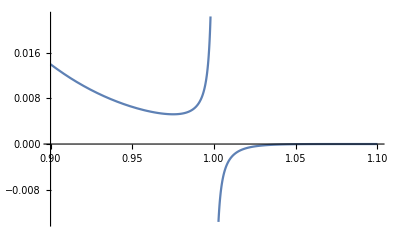

```mathematica
Plot[I*EDtermuda[-0.01,0.1,-1],{y,1-0.1,1+0.1}]
```

```mathematica
NIntegrate[1/x,{x,-0.1,-0.00000000000000000000001}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.89338×10^-16}. NIntegrate obtained -50.7925 and 1.63523 for the integral and error estimates.

-50.7925

```mathematica
1/x/.{x->-0.00000001}
```

-1.×10^8

```mathematica
NIntegrate[1/x,{x,0.00000001,0.1}]
```

16.1181

```mathematica
NIntegrate[1/x,{x,-0.1,0}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.63073×10^-30}. NIntegrate obtained -757.365 and 296.932 for the integral and error estimates.

-757.365

```mathematica
NIntegrate[1/x,{x,0,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.63073×10^-30}. NIntegrate obtained 757.365 and 296.932 for the integral and error estimates.

757.365

```mathematica
NIntegrate[1/x,{x,-0.1,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.63073×10^-30}. NIntegrate obtained 757.365 and 296.932 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand 1/x is being considered as zero over the specified region, but may actually be divergent.

0.